# Regression modelling of rank-deficient precision matrix

## Generate data

```mathematica
(* Batch dimension is last one *)
n=2;
e=0.01;
trueCov={{1, 1-e},{1-e,1}};
zero=0&/@Range@n;
normal=MultinormalDistribution[zero,trueCov];
pdf[x_,y_]=PDF[normal,{x,y}];
dsize=1000;
SeedRandom[0];
X=RandomVariate[normal,{dsize}]//Transpose;
(* center the data *)
Xc=Mean[Transpose@X];
X=Transpose[#-Xc&/@Transpose[X]];
wt = {{1,1}}; (* true w *)
w0={{2,1}}; (* initial w *)
Y=Dot[wt, X];
XY = X~Join~Y;
grad[w_]:=2(w.X-Y).Transpose[X]/dsize;
loss[w_]:=Module[{error},
error=(w.X-Y);
First[Flatten[error.errorᵀ/dsize]]
];
Print["Loss at w0 ",loss[w0]];
Print["Grad at w0 ",grad[w0]];
cov=X.Xᵀ/dsize; 
cov2=X.Xᵀ/(dsize-1); (* unbiased estimate *)
(* sanity checks *)
Print["True cov ",MatrixForm@trueCov];
Print["Data cov ", MatrixForm@cov];
Print["Data mean ", Mean@Transpose@X];

(* Augment with third component being sum of first two *)
Xa= X~Join~{{1,1}.X };
wta=Join[wt,{{0}}, 2];
w0a=Join[w0,{{0}}, 2];
Ya=Dot[wta, Xa];
XYa = Xa~Join~Ya;

cova=Xa.Xaᵀ/dsize; 
cov2a=Xa.Xaᵀ/(dsize-1); (* unbiased estimate *)


grada[wa_]:=2(wa.Xa-Ya).Transpose[Xa]/dsize;
lossa[wa_]:=Module[{error},
error=(wa.Xa-Ya);
First[Flatten[error.errorᵀ/dsize]]
];
Print["Augmented loss ",lossa[w0a]]
Print["Augmented grad ",grada[w0a]]
```

Loss at w0 1.03475

Grad at w0 {{2.06949,2.05021}}

True cov (1 | 0.99
0.99 | 1)

Data cov (1.03475 | 1.02511
1.02511 | 1.03619)

Data mean {-2.45359×10^-17,1.98286×10^-16}

Augmented loss 1.03475

Augmented grad {{2.06949,2.05021,4.11971}}

```mathematica
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimize[loss_,grad_,w0_,pre_,lr_]:=Module[{gradstep},
gradstep[w_]:=w-lr*grad[w].pre;
points=NestList[gradstep,w0,100];
loss/@points
];

losses0=optimize[loss,grad,w0,IdentityMatrix[2],.15];
losses1=optimize[lossa,grada,w0a,IdentityMatrix[3],.15];
```

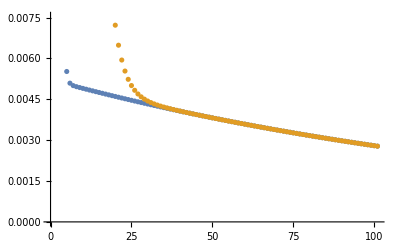

```mathematica
ListPlot[{losses0,losses1}]
```

## Modified Cholesky decomposition

```mathematica
Ch=CholeskyDecomposition@cov//Transpose;
Ch//MatrixForm
```

(1.01722 | 0.
1.00775 | 0.143648)

```mathematica
Cha=CholeskyDecomposition@cova
```

CholeskyDecomposition::posdef: The matrix {{1.03475,1.02511,2.05985},{1.02511,1.03619,2.0613},{2.05985,2.0613,4.12115}} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition[{{1.03475,1.02511,2.05985},{1.02511,1.03619,2.0613},{2.05985,2.0613,4.12115}}]

### Have to use SVD to get Cholesky decomposition

```mathematica
{u,s,v}=SingularValueDecomposition@cova
```

{{{-0.408105,0.70719,0.57735},{-0.408392,-0.707024,0.57735},{-0.816497,0.00016575,-0.57735}},{{6.18173,0.,0.},{0.,0.010362,0.},{0.,0.,0.}},{{-0.408105,0.70719,-0.57735},{-0.408392,-0.707024,-0.57735},{-0.816497,0.00016575,0.57735}}}

```mathematica
MatrixForm/@{u,v}
```

{(-0.408105 | 0.70719 | 0.57735
-0.408392 | -0.707024 | 0.57735
-0.816497 | 0.00016575 | -0.57735),(-0.408105 | 0.70719 | -0.57735
-0.408392 | -0.707024 | -0.57735
-0.816497 | 0.00016575 | 0.57735)}

```mathematica
u-v//Chop//MatrixForm
```

(0 | 0 | 1.1547
0 | 0 | 1.1547
0 | 0 | -1.1547)

```mathematica
u.s.Transpose[v]-cova//Chop//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
u.s.Transpose[u]-cova//Chop//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
{q,r}=QRDecomposition[Sqrt[s].Transpose[u]];
MatrixForm/@{q,r}
```

{(-0.997493 | 0.0707686 | 0.
0.0707686 | 0.997493 | 0.
0. | 0. | 1.),(1.01722 | 1.00775 | 2.02497
0. | -0.143648 | -0.143648
0. | 0. | 0.)}

```mathematica
rᵀ.r-cova//Chop//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
Cha=rᵀ
```

{{1.01722,0.,0.},{1.00775,-0.143648,0.},{2.02497,-0.143648,0.}}

```mathematica
Cha//MatrixForm
```

(1.01722 | 0. | 0.
1.00775 | -0.143648 | 0.
2.02497 | -0.143648 | 0.)

```mathematica
Cha.Chaᵀ-cova//Chop//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
D1a=DiagonalMatrix@Diagonal@Cha
```

{{1.01722,0.,0.},{0.,-0.143648,0.},{0.,0.,0.}}

```mathematica
Dia=DiagonalMatrix[If[Abs[#]>1*^-9,1/#,#]&/@Diagonal@Cha]
```

{{0.983067,0.,0.},{0.,-6.96147,0.},{0.,0.,0.}}

```mathematica
La=Cha.Dia;
La//MatrixForm
```

(1. | 0. | 0.
0.990685 | 1. | 0.
1.99068 | 1. | 0.)

```mathematica
Ta=PseudoInverse@La;
Ta//MatrixForm
```

(0.666667 | -0.333333 | 0.333333
-0.99379 | 0.996895 | 0.00310509
0. | 0. | 0.)

```mathematica
PseudoInverse[cova]//MatrixForm
```

(48.2915 | -48.2263 | 0.0652155
-48.2263 | 48.2689 | 0.0426318
0.0652155 | 0.0426318 | 0.107847)

```mathematica
cova//MatrixForm
```

(1.03475 | 1.02511 | 2.05985
1.02511 | 1.03619 | 2.0613
2.05985 | 2.0613 | 4.12115)

```mathematica
cov
```

{{1.03475,1.02511},{1.02511,1.03619}}

```mathematica
trueCov
```

{{1,0.99},{0.99,1}}

```mathematica
{{2, 1}, {1, 2}}
```

```mathematica
dummy=({{2, 1, 1}, {1, 1, 1}, {1, 1, 1}})
```

{{2,1,1},{1,1,1},{1,1,1}}

```mathematica
dummy//Eigenvalues
```

{2+√2,2-√2,0}

```mathematica
PseudoInverse@dummy//MatrixForm
```

(1 | -1/2 | -1/2
-1/2 | 1/2 | 1/2
-1/2 | 1/2 | 1/2)

## Try SGD with pseudo - inverse

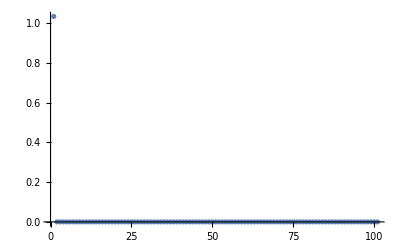

```mathematica
(* Newton's method on original problem *)
losses2=optimize[loss,grad,w0,Inverse[cov],.5];
ListPlot@losses2
```

```mathematica
(* Newton's method on augmented problem *)
losses3=optimize[lossa,grada,w0a,PseudoInverse[cova],.5];
ListPlot@losses3
```

-Graphics-

## Try SGD with regularized inverse

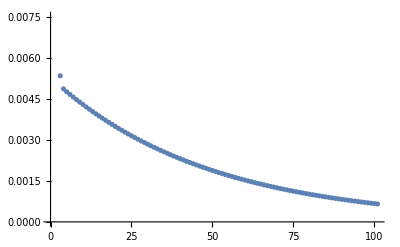

```mathematica
(* Newton's method on augmented problem *)
losses3=optimize[lossa,grada,w0a,Inverse[cova+IdentityMatrix[3]],.5];
ListPlot@losses3
```

## Fix data for linear-rankdeficient.py

```mathematica
(* must manually edit the file to get rid of closing bracket*)
Export["~/git/whitening/exp/linear-rankdeficient-losses-pre-fixed.csv",losses3]
```

~/git/whitening/exp/linear-rankdeficient-losses-pre-fixed.csv

```mathematica
Export["~/git/whitening/exp/linear-rankdeficient-fixed.csv",XYa];
```

```mathematica
losses3//First
```

1.03475

```mathematica
PseudoInverse[cova]
```

{{48.2915,-48.2263,0.0652155},{-48.2263,48.2689,0.0426318},{0.0652155,0.0426318,0.107847}}

```mathematica
data=Import["~/git/whitening/exp/mnist_small.csv"];
```

```mathematica
data//Dimensions
```

{59,1000}